Initialisation cells

### Standard commands

```mathematica
mult[λ_] := Plus @@ λ!/Product[
     (λ[[Length[λ] - a]] + a)!/
      Product[λ[[Length[λ] - a]] - 
        λ[[Length[λ] - k]] + (a - k), 
       {k, 0, a - 1}], {a, 0, Length[λ] - 1}]; 
DualDiagram[λ_] := Total /@ Transpose[
     (PadRight[#1, λ[[1]]] & ) /@ 
      (ConstantArray[1, #1] & ) /@ λ]; 
ToYD[stb_]:=Length/@stb;
CheckStandard[λT_] := 
   And @@ Flatten[{Table[λT[[a - 1,s]] < 
        λT[[a,s]], {a, 2, Length[λT]}, 
       {s, 1, Length[λT[[a]]]}], 
      Table[λT[[a,s - 1]] < λT[[a,s]], 
       {a, 1, Length[λT]}, {s, 2, 
        Length[λT[[a]]]}], Sort[Flatten[λT]] == 
       Range[Length[Flatten[λT]]], 
      ListQ /@ λT}];
```

```mathematica
Wronsk[A_, B_] := (A /. u -> u + I/2)*
     (B /. u -> u - I/2) - (A /. u -> u - I/2)*
     (B /. u -> u + I/2); 
toMonic[A_] := Collect[
    (#1/Coefficient[#1, u, Exponent[#1, u]] & )[
     Expand[A]], u];
```

```mathematica
mPrint[x___]:=Print[x];
PrintDone[x_]:=mPrint["...Done in: ",Timing[x][[1]],"s"];
SetAttributes[PrintDone,HoldAll];
```

### Q-system on Young diagram

GenerateQsystem generates all QQ-relations. Input is  λ - a Young diagram, you can also tinker with the code and specify Domain of interest (collection of {a,s} specifying which QQ-relations to take into account). The other code is compatible with this specification.

```mathematica
GenerateQsystem[λ_]:=Block[{},
(mPrint["Generating QQ relations on Young diagram..."];
(* Length of spin chain *)
Len=Total[λ];
Unprotect[M];ClearAll[M];(* Unprotecting because of conflict with Combinatorica package *)
(* domain of interest is the values of {a,s} for which we are going to check QQ relation with Q[a,s] in the top left corner (smallest a,s)
FullYoungDiagram - is maximal possible domain of interest*)
FullYoungDiagram=Block[{mm},Flatten@Table[mm[a,s],{a,0,Length[λ]-1},{s,0,λ[[a+1]]-1}]/.mm->List];
DomainOfInterest=FullYoungDiagram;
(* comment below provides some example of non-standard DomainOfInterest *)
(*DomainOfInterest=Block[{mm},Flatten@Table[mm[a,s],{a,0,1},{s,0,1}]/.mm->List];*)
M[a_,s_]:=M[a,s]=Len+a s-Total[λ[[1;;a]]]-Total[DualDiagram[λ][[1;;s]]];
YQa[0,0]:=u^Len+Sum[u^(Len-k)sym[k],{k,Len}];
YQa[a_,s_]:=u^M[a,s]+Sum[c[a,s,k] u^(M[a,s]-k),{k,M[a,s]}];
YQθ[0,0]=YQa[0,0];
YQθ[a_,s_]:=Product[u-qθ[a,s,k],{k,1,M[a,s]}];
QQrel[a_,s_]:=
CoefficientList[(YQa[a,s]/.u->u+I/2)(YQa[a+1,s+1]/.u->u-I/2)-(YQa[a,s]/.u->u-I/2)(YQa[a+1,s+1]/.u->u+I/2)-I(M[a,s]-M[a+1,s+1])YQa[a+1,s]YQa[a,s+1],u]//(#/.Complex[0,b_]:>b)&;
Allrel=Monitor[Table[If[MemberQ[DomainOfInterest,{a,s}]&&M[a,s]>0,QQrel[a,s],Nothing],{a,0,Length[λ]-1},{s,0,λ[[a+1]]-1}],{a,s}]//Flatten;
(* vars have coefficients of all Q-functions *)
vars=Table[If[a+s==0,Nothing,c[a,s,k]],{a,0,Length[λ]-1},{s,0,λ[[a+1]]-1},{k,M[a,s]}]//Flatten;
(* only those appearing in domain of interest *)
vars2=DeleteCases[Variables[Allrel],sym[_]];
mPrint@Column[{
Row@{"Length of spin chain: ",Len},
Row@{"Number of SYT: ",mult[λ]},
Row@{"Domain of Interest: ",MatrixPlot[#,Mesh->True]&@Table[Which[MemberQ[DomainOfInterest,{a,s}],1,MemberQ[FullYoungDiagram,{a,s}],1/2,True,0],{a,0,Length[λ]-1},{s,0,λ[[1]]-1}]},
Row@{"Number of variables: ",Length[vars2]},
Row@{"Number of equations: ",Length[Allrel]}
}];
)//PrintDone
];
```

### Choice of SYT and initial conditions

showSYT will draw SYT with λT as global area. Shaded region is decided domain of interest

```mathematica
showSYT[λT_] := Graphics[
    Table[{Text[Style[λT[[a,s]], Small, Black], 
       {s, -a}], Opacity[0.5], Lighter[Lighter[Gray]], 
      Rectangle[{s - 1/2, -a - 1/2}]}, {a, 1, Length[λT]}, 
     {s, 1, Length[λT[[a]]]}], ImageSize -> Tiny]; 
(* Next command includes domain of interest *)
showSYT[λT_,"DOI"]:=Graphics[
    Table[{Text[Style[λT[[a,s]], Small, Black], 
       {s, -a}], Opacity[0.5], Lighter[Lighter[Gray]], 
      Rectangle[{s - 1/2, -a - 1/2}], 
      If[MemberQ[DomainOfInterest, {a - 1, s - 1}], 
       {Gray, Rectangle[{s - 1/2, -a - 1/2}]}, 
       Nothing]}, {a, 1, Length[λT]}, 
     {s, 1, Length[λT[[a]]]}], ImageSize -> Tiny];
```

Solution of Q-system in the large Λ limit, the leading order

```mathematica
initθrep[λT_] := initθrep[λT] = 
   Block[{kk, sd}, kk[_, _] = 0; sd[m_] := 
      (Select[#1, #1 <= m & ] & ) /@ λT; 
     If[CheckStandard[λT], 
      Sort[Flatten[Table[Table[If[True || 
            MemberQ[DomainOfInterest, {a2, s2}], 
           qθ[a2, s2, ++kk[a2, s2]] -> 
            Product[(Length[sd[λT[[a,s]]][[a3]]] + a - 
                s - a3)/(Length[sd[λT[[a,s]]][[a3]]] + 
                a - s - a3 + 1), {a3, 1, a2}]*
             Product[(DualDiagram[Length /@ sd[λT[[a,
                   s]]]][[s3]] + s - a - s3)/(
                DualDiagram[Length /@ sd[λT[[a,s]]]][[
                 s3]] + s - a - s3 + 1), {s3, 1, s2}]*
             θ[λT[[a,s]]], Nothing], {a2, 0, a - 1}, 
          {s2, 0, s - 1}], {a, 1, Length[λT]}, 
         {s, 1, Length[λT[[a]]]}]]], 
      Print["Not standard tableau"]; ]]
```

Generating system of relations with leading coefficient plugged in. Working only up to maxord (I think I overdo one order)

```mathematica
LargeΛExpansion:=Block[{},
(mPrint["1/Λ expansion of QQ system around the chosen SYT solution..."];
showSYT[λT]//mPrint;
Λinitθrep=initθrep[λT]/.θ[i_]:>Λ^i;
fsymrep=Table[sym[n]->Expand@Coefficient[Product[u-Λ^i,{i,Len}],u,Len-n],{n,Len}];
finitθrep=Λinitθrep;(* definition for forward compatibility *)
ftransit=Solve[(Table[If[a+s==0||Not@MemberQ[vars2,c[a,s,1]],Nothing,CoefficientList[YQa[a,s]-(YQθ[a,s]/.Λinitθrep),u]],{a,0,Length[λ]-1},{s,0,λ[[a+1]]-1}]//Flatten)==0,vars2][[1]];
Λtransit=Thread[Rule[ftransit[[All,1]],(#/.Λ^(pow_/;pow<Exponent[#,Λ]-maxord):>0)&/@ftransit[[All,2]]]];
(* choosing special parameterisation of inhomogeneities *)
symrep=Table[sym[n]->Expand@Coefficient[Product[u-Λ^i,{i,Len}],u,Len-n]/.Λ^(pow_/;pow< n/2(2Len-n+1)-maxord):>0,{n,Len}];
anlytic=Collect[(Allrel/.symrep/.c[a_,s_,k_]:>(1+ecc[a,s,k]/Λ)c[a,s,k]/.Λtransit)//Expand,Λ];
)//PrintDone;
"Check on genereated equations: "If[((Exponent[anlytic,Λ]//Min)>0),"passed"]//mPrint;
];
```

Generating list of subleading equations and solving them.

```mathematica
SubleadingOrders:=Block[{},
(mPrint["Arranging and solving 1/Λ analytic equations for c..."];
sublead=Monitor[Table[Normal@Series[(#/Λ^Exponent[#,Λ])&[anlytic[[k]]],{Λ,∞,maxord}],{k,Length[anlytic]}],k];
cutoff=Series[Λ,{Λ,∞,maxord-1}]-Λ;
subleadingeqns=Monitor[Table[(sublead[[k]]/.ecc[a_,s_,k_]:>Sum[(ecc[ord][a,s,k])/Λ^(ord-1),{ord,1,maxord}]+cutoff)[[3]],{k,Length[sublead]}],k];
Do[Λsol[ord]=Solve[subleadingeqns[[All,ord]]==0/.Flatten@Table[Λsol[k],{k,ord-1}],vars2/.c[a_,s_,k_]:>ecc[ord][a,s,k]][[1]],{ord,maxord}];
;)//PrintDone
]
```

### Numerical iterations

```mathematica
GenerateEqnsForNumerics:=Block[{},
(mPrint["Generating equations for numerical iterations"];
(* normalised variables and equations, max powers of Λ are taken out *)
nvars=vars2/.c->nc;
sym2nsym=Table[sym[n]->Λ^(n(2Len-n+1)/2)nsym[n],{n,Len}];
nsym2sym=Table[nsym[n]->Λ^(-n(2Len-n+1)/2)sym[n],{n,Len}];
vars2nvars=Thread[Rule[vars2,vars2/.c[a_,s_,k_]:>(Λ^Exponent[c[a,s,k]/.ftransit,Λ] nc[a,s,k])]];
nvars2vars=Thread[Rule[nvars,vars2/.c[a_,s_,k_]:>(Λ^(-Exponent[c[a,s,k]/.ftransit,Λ])c[a,s,k])]];
nfsymrep=Thread[Rule[fsymrep[[All,1]]/.sym->nsym,Collect[# Λ^(-Exponent[#,Λ])&/@fsymrep[[All,2]],Λ]]];
nftransit=Thread[Rule[ftransit[[All,1]]/.c->nc,Collect[# Λ^(-Exponent[#,Λ])&/@ftransit[[All,2]],Λ]]];
(* these is the rescaled version of equations *)
NormedEqns=Collect[# Λ^(-Exponent[#,Λ])&/@(Allrel/.vars2nvars/.sym2nsym),Λ];
)//PrintDone;
]
```

```mathematica
(* generating equations using asymptotic approximation *)
AsymEqns[Λ0_]:=Block[{},
nsymrep=nfsymrep/.Λ->Λ0;
ntransit=nftransit/.Λ->Λ0;
subnc=
Thread[Rule[nvars,nvars/.(nc[a_,s_,k_]:>(1+1/Λ0 Sum[1/Λ0^(ord-1)(ecc[ord][a,s,k]/.Λsol[ord]),{ord,1,maxord}])nc[a,s,k])/.ntransit]];
#/(1+Abs[#/.nc[a_,s_,k_]:> (nc[a,s,k]/.subnc)])&/@(NormedEqns/.nsymrep/.Λ->Λ0)//Expand
];
(* generating equations using previous order results and polynomial fit *)
InterpEqns[Λ0_]:=Block[{minterpord=Min[Length[Λvals]-1,interpord]},
nsymrep=nfsymrep/.Λ->Λ0;
subnc=
Thread[Rule[nvars,Round[Sum[(nvars/.sol[Λvals[[-j]]])Product[If[j==j2,1,(Λ0-Λvals[[-j2]])/(Λvals[[-j]]-Λvals[[-j2]])],{j2,minterpord}],{j,minterpord}],10^-prec]]];
#/(#/.nc[a_,s_,k_]:> ((1+Round[Random[]/100,10^-5])nc[a,s,k]/.subnc))&/@(NormedEqns/.nsymrep/.Λ->Λ0)//Expand
];
(* Routine to produce solution *)
FindSol:=(i=0;{minim,minsolrep}=Monitor[FindMinimum[normedrel.normedrel,{nvars,nvars/.subnc}//Transpose,WorkingPrecision->prec,PrecisionGoal->Infinity,AccuracyGoal->prec/2,MaxIterations->50,Method->Automatic,EvaluationMonitor:>(i++;norm=normedrel.normedrel//N;If[i>MyMaxIterations,Throw["Too big step"]])],Row@{"Step: " ,i,",   Minim: ",norm}]);
SilentFindSol:=(i=0;{minim,minsolrep}=FindMinimum[normedrel.normedrel,{nvars,nvars/.subnc}//Transpose,WorkingPrecision->prec,PrecisionGoal->Infinity,AccuracyGoal->prec/2,MaxIterations->50,Method->Automatic,EvaluationMonitor:>(i++;If[i>MyMaxIterations,Throw["Too big step"]])]);
```

```mathematica
(* solving first point solution, to decide where to start *)
SolveAtΛ0:=Block[{},
mPrint["Checking if can solve at Λ0. If this produces mistakes, increase Λ0"];
i=0;
normedrel=AsymEqns[Λ0];
FindSol;
minim//N//mPrint;
]
```

```mathematica
(* generating first sample points for interpolation to work + some large Λ expressions *)
GenerateSolsFromAsymptotics:=Block[{},
mPrint["Initialise: Numerical solutions from analytic 1/Λ approximation"];
Λvals0={};
rng=Join[Range[Λ0,Λ0+(startinterpord-1) 1/40,1/40]]//Flatten//Union//Sort//Reverse;
Monitor[Do[
normedrel=AsymEqns[Λ0];
FindSol;
(*sol[Λ0]:=Thread[Rule[vars2,(vars2/.subc)(vars3/.minsolrep)]];*)
sol[Λ0]=minsolrep;
AppendTo[Λvals0,Λ0];
,{Λ0,rng}],Row@{"Current Λ is: ",Λ0//N}]
]//PrintDone;
```

```mathematica
(* Iteration procedure *)
Iterate:=Block[{},
mPrint["Numerical iterations towards Λ=",Λtarget];
mPrint["If step becomes below 10^-7, try to increase prec"];
pp=pmin;qq=1;
step:=qq/base^pp;
(* starting the procedure *)
ΛLast=Λvals[[-1]];
Monitor[
While[ΛLast>Λtarget,
Λnew=Max[ΛLast-step,Λtarget];
normedrel=InterpEqns[Λnew];
Which[
Catch[SilentFindSol]==="Too big step",
pp=pp+1,
i>5,
sol[Λnew]=minsolrep;
AppendTo[Λvals,Λnew]
,
True,
sol[Λnew]=minsolrep;
AppendTo[Λvals,Λnew];
If[pp>pmin,qq=qq+Δq;If[qq==base,qq=1;pp=pp-1]];
];
ΛLast=Λvals[[-1]]
],
Row@{"Current Λ is: ",ΛLast//N,"   step is: ",step//N}]//PrintDone;
mPrint["Finished iterations. List of all Λ computed: ", Λvals//N];
];
```

Relating to rigged configurations

### Inits

```mathematica
(* Loading rigged configurations package *)
SetDirectory[NotebookDirectory[]]
<<RC.m;
(* Path ↔ Tableaux *)
ToCrystalPath[stb_]:=Block[{len=Length[stb//Flatten]},Table[{{Position[stb,k][[1,1]]}},{k,len}]];
ToTableau[path_]:=Block[{pr=path//Flatten,max},max=Max[pr];
Table[Position[pr,k]//Flatten,{k,max}]];
Quiet[Needs["Combinatorica`"]];
(* Generating rigged *)
ToRigged[SYT_,n_:5]:=rkkrec[ToCrystalPath[SYT],n];
(* generating SYT from rigged *)
ToSYT[rigged_]:=ToTableau[kkrrec[ConstantArray[{1,1},Length[rigged[[1,1]]]],rigged[[2;;3]]]];
```

/home/zuxian/Documents/BAE

### Examples

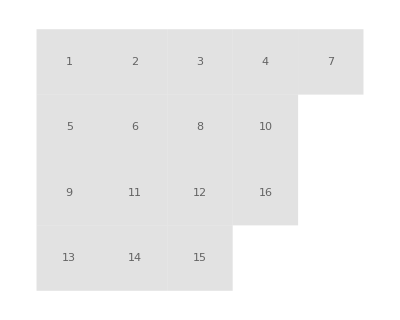

```mathematica
YD={5,4,4,3}; (* choose shape *)
(SYT=RandomTableau[YD]);
showSYT[SYT]
```

```mathematica
SYT//ToRigged//showRC
```

-Graphics- | -Graphics- | -Graphics- | ∅ | ∅

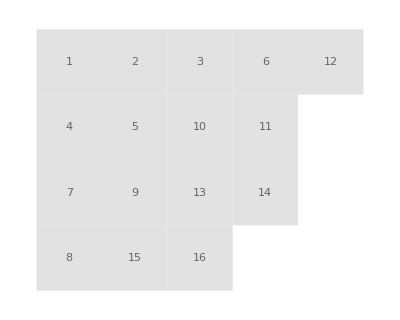

```mathematica
(rigged={{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{{4,2,2,2,1},{4,2,1},{3},{},{}},{{0,3,3,1,4},{0,1,0},{0},{},{}}})//showRC
rigged//ToSYT//showSYT
```

Usage

### Parameters to control computation

```mathematica
maxord=5; (* Number of orders in analytic 1/Λ expansion of large θ solution. Generation of each next order is time-costly.  Roughly, the lower maxord is the bigger Λ0 is needed *)
Λ0=4; (* use analytic expressions as a solution guess for Λ≥Λ0. Large Λ may need larger prec. May need Λ0=4 for big systems *)
prec=40; (* Precision to use in computations. If iteration step drops below 10^-6, try increasing precision. Until length 16 prec=40 should be ok, then need prec=80 sometimes. After length 20, need play more seriously with prec *)
interpord=25; (* how many points from previous computations to take to guess the next step. Seriously affects convergence speed. Good values are between approx. 20 and 40 and depend on solution. *)
startinterpord=10; (* how many points to generate from asymptotic solution *)
$MaxPrecision=Infinity;(* I don't remember why I neded this. Maybe already irrelevant *)
MyMaxIterations=12; (* Number of iterations before aborting attempts to converge. *) 
base=2;pmin=3;RecoverySpeed=1/3;
Δq=(base-1)Min[1,RecoverySpeed];(* step of iteration is computed as q/base^p and it is automatically adjusted: q->q+Δq if converges fast; p->p+1 if computation aborts; q->1,p->p-1 if q=base *)
(* increase base and/or pmin if you want to reduce maximal allowed step *)
Λtarget=1; (* when to terminate iteration *)
```

### Solving

#### Inits

```mathematica
SolutionFromSYT[SYT_]:=Block[{},
λT=SYT;
λ=SYT//ToYD;
GenerateQsystem[λ];
LargeΛExpansion;
SubleadingOrders;
GenerateEqnsForNumerics;
SolveAtΛ0;
GenerateSolsFromAsymptotics;
Λvals=Λvals0;
(* the previous line resets Λvals - a record for which Λ solution was already found *)
Iterate
];
```

Generating QQ relations on Young diagram...

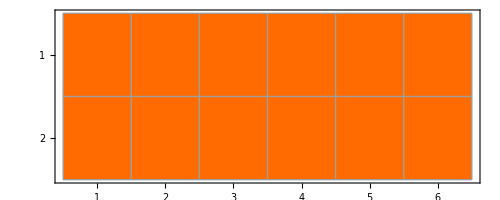
Length of spin chain: 12
Number of SYT: 132
Domain of Interest: -Graphics-
Number of variables: 51
Number of equations: 66

...Done in: 0.142719s

1/Λ expansion of QQ system around the chosen SYT solution...

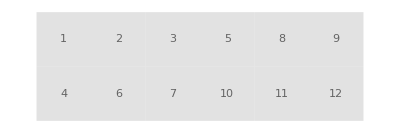

...Done in: 0.244999s

Check on genereated equations:  passed

Arranging and solving 1/Λ analytic equations for c...

...Done in: 8.82978s

Generating equations for numerical iterations

...Done in: 0.011534s

Checking if can solve at Λ0. If this produces mistakes, increase Λ0

2.166×10^-47

Initialise: Numerical solutions from analytic 1/Λ approximation

...Done in: 1.76156s

Numerical iterations towards Λ=1

If step becomes below 10^-7, try to increase prec

...Done in: 8.12412s

Finished iterations. List of all Λ computed: {4.225,4.2,4.175,4.15,4.125,4.1,4.075,4.05,4.025,4.,3.875,3.75,3.625,3.5,3.375,3.25,3.125,3.,2.875,2.75,2.625,2.5,2.375,2.25,2.125,2.,1.875,1.75,1.625,1.5,1.375,1.3125,1.25,1.1875,1.17188,1.15625,1.13542,1.11458,1.09375,1.08854,1.08203,1.07422,1.0638,1.05078,1.03516,1.01953,1.00391,1.}

```mathematica
SolutionFromSYT[{{1,2,3,5,8,9},{4,6,7,10,11,12}}]
```

Generating QQ relations on Young diagram...

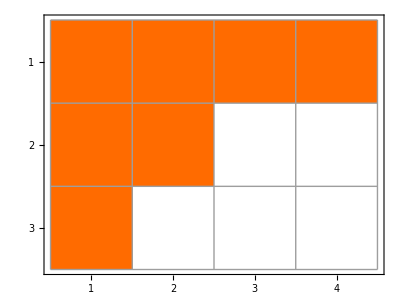
Length of spin chain: 7
Number of SYT: 35
Domain of Interest: -Graphics-
Number of variables: 12
Number of equations: 13

...Done in: 0.013467s

1/Λ expansion of QQ system around the chosen SYT solution...

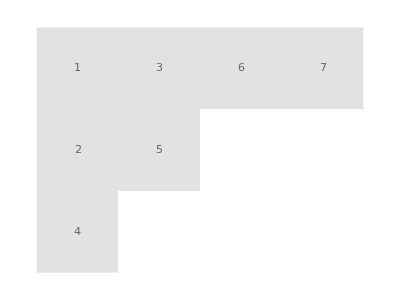

...Done in: 0.02366s

Check on genereated equations:  passed

Arranging and solving 1/Λ analytic equations for c...

...Done in: 0.042608s

Generating equations for numerical iterations

...Done in: 0.001556s

Checking if can solve at Λ0. If this produces mistakes, increase Λ0

6.8662×10^-54

Initialise: Numerical solutions from analytic 1/Λ approximation

...Done in: 0.113002s

Numerical iterations towards Λ=1

If step becomes below 10^-7, try to increase prec

...Done in: 0.147007s

Finished iterations. List of all Λ computed: {4.225,4.2,4.175,4.15,4.125,4.1,4.075,4.05,4.025,4.,3.875,3.75,3.625,3.5,3.375,3.25,3.125,3.,2.875,2.75,2.625,2.5,2.375,2.25,2.125,2.,1.875,1.75,1.625,1.5,1.375,1.25,1.125,1.}

Generating QQ relations on Young diagram...

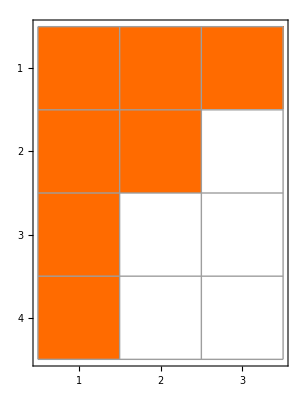
Length of spin chain: 7
Number of SYT: 35
Domain of Interest: -Graphics-
Number of variables: 12
Number of equations: 13

...Done in: 0.013547s

1/Λ expansion of QQ system around the chosen SYT solution...

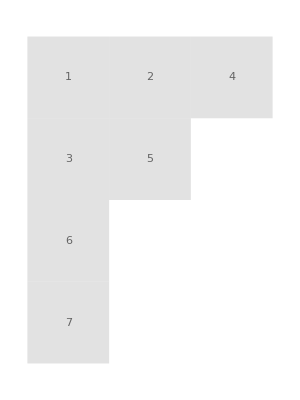

...Done in: 0.026743s

Check on genereated equations:  passed

Arranging and solving 1/Λ analytic equations for c...

...Done in: 0.282672s

Generating equations for numerical iterations

...Done in: 0.001441s

Checking if can solve at Λ0. If this produces mistakes, increase Λ0

6.8662×10^-54

Initialise: Numerical solutions from analytic 1/Λ approximation

...Done in: 0.118639s

Numerical iterations towards Λ=1

If step becomes below 10^-7, try to increase prec

...Done in: 0.138207s

Finished iterations. List of all Λ computed: {4.225,4.2,4.175,4.15,4.125,4.1,4.075,4.05,4.025,4.,3.875,3.75,3.625,3.5,3.375,3.25,3.125,3.,2.875,2.75,2.625,2.5,2.375,2.25,2.125,2.,1.875,1.75,1.625,1.5,1.375,1.25,1.125,1.}

```mathematica
SolutionFromSYT[{{1,3,6,7},{2,5},{4}}];
SolutionFromSYT@{{1,2,4},{3,5},{6},{7}}
```

```mathematica
SolutionFromSYT[{{1,3,6,7},{2,5},{4}}];
```

```mathematica
SolutionFromSYT@{{1,2,4},{3,5},{6},{7}};
```

```mathematica
DomainOfInterest
```

```mathematica
Λval = 1;   (* use solution at Λ = 1 *)
(* 1. Convert normalized coefficients nc -> c *)
subRules = sol[Λval] /. nc -> c;
(* 2. Compute Q_{a,0}(u) for a = 1,2 *)
Qs = Table[YQa[a, 0] /. subRules, {a, 1}];
(* 3. Make them monic (divide by leading coefficient) *)
monicQs = toMonic /@ Qs;
(* 4. Expand to clean the expressions *)
monicQs // Expand

betheRoots=NSolve[#==0,u]&/@monicQs;
betheRoots=(u/. NSolve[#==0,u])&/@monicQs-1
```

{2.353716985014337404389079278080168196085-11.14695853216081173695106632205391338615 u+22.41824676207743672238194600609535429426 u^2-24.85438955535406512612333502383410809326 u^3+16.22890610556096614909828600921210717208 u^4-6. u^5+u^6}

{{-0.17458378470878500486687992957477614,0.01075711870492310738269741642811965,0.01249979161500916529084491858035388-0.999589013956466780185290734969567441 ⅈ,0.01249979161500916529084491858035388+0.999589013956466780185290734969567441 ⅈ,0.06941354138692178345124633799297437-0.49999999999983476612201607106696552 ⅈ,0.06941354138692178345124633799297437+0.49999999999983476612201607106696552 ⅈ}}

```mathematica
betheRoots//Round[#,10^-3]&//N
```

{{-0.175,0.011,0.012-1. ⅈ,0.012+1. ⅈ,0.069-0.5 ⅈ,0.069+0.5 ⅈ}}

```mathematica
Qs = Table[YQa[DomainOfInterest[[a,1]],DomainOfInterest[[a,2]]] /. subRules,  {a,2,Length@DomainOfInterest}]
```

{2.095443360958478168470468035186252562358-7.336882613133856579276384430698582555206 u+9.314604610020906302301440984449757134782 u^2-5.076401130770137975888464003249908470042 u^3+u^4,2.401083032164779318893718483066105134907-3.175525285846140020186353775819615996004 u+u^2,-1.587762642923070010093176887909807998002+u,-0.1499763513453125712733465562632287538014+0.9403289616690042965397922072095365951159 u-1.49400369183323606279652926113754277939 u^2+u^3,-0.6317755622314634617299942266178153565286+u,-0.3642268989906939134676919474738798297356+u}

```mathematica
YQa[{0,1}//Flatten]
```

YQa[{0,1}]

```mathematica
Λval = 1;   (* use solution at Λ = 1 *)
(* 1. Convert normalized coefficients nc -> c *)
subRules = sol[Λval] /. nc -> c;
(* 2. Compute Q_{a,0}(u) for a = 1,2 *)
Qs = Table[YQa[DomainOfInterest[[a,1]],DomainOfInterest[[a,2]]] /. subRules,  {a,2,Length@DomainOfInterest}]
(* 3. Make them monic (divide by leading coefficient) *)
monicQs = toMonic /@ Qs;
(* 4. Expand to clean the expressions *)
monicQs // Expand

betheRoots=NSolve[#==0,u]&/@monicQs;
betheRoots=(u/. NSolve[#==0,u])&/@monicQs-1
```

{-0.02539108448434437825793447947291578716123-1.908137510806502179790032834408052589908 u+16.06106031236448185174528888360151688565 u^2-59.48405827968080377471187349250980369521 u^3+130.4132685746483735223470675289225900971 u^4-185.45360551193355698797980690480682087 u^5+175.6854435563497137883011660647634309238 u^6-110.0416029841845528211076185646188262591 u^7+43.75301341349129055012881628439827040399 u^8-10. u^9+u^10,-0.09202777906611886638762477268356646319118-2.2329999962038475286585933096171628356 u+12.05261305569024081333635957883723534556 u^2-32.34426343738118640606070913846871093039 u^3+50.84633314268461574766151463589516874492 u^4-48.04992358102146338532914227754259151088 u^5+26.67148812825273154687277272170389931305 u^6-8. u^7+u^8,0.6381250810560343064881742548891643329315-3.928356372083505631317732567102310875651 u+11.00440856140695554209851226619462752839 u^2-17.03744268576609753899685670815694363316 u^3+14.25542414428432299023186931191688672718 u^4-6. u^5+u^6,1.26705569506454382379030147826970699577-4.016641193673821128443047425847530503628 u+6.004821461586064880206106055037232646382 u^2-4. u^3+u^4,1.419680080157957216795482951064937070656-2. u+u^2,2.353716985014337404389079278080168196085-11.14695853216081173695106632205391338615 u+22.41824676207743672238194600609535429426 u^2-24.85438955535406512612333502383410809326 u^3+16.22890610556096614909828600921210717208 u^4-6. u^5+u^6,-0.8847268572203825759033720943492310604731+4.830431236432317882610934333829766902742 u-9.927194777677032563061667511917054046628 u^2+9.985937403707310766065524006141404781385 u^3-5. u^4+u^5,0.4792893771010980382189106664588831414791-2.970877911070813025224667004766821618651 u+5.491562442224386459639314403684842868831 u^2-4. u^3+u^4,-0.4927194777677032563061667511917054046628+2.495781221112193229819657201842421434415 u-3. u^2+u^3,0.7485937403707310766065524006141404781385-2. u+u^2,-1.+u}

{-0.02539108448434437825793447947291578716123-1.908137510806502179790032834408052589908 u+16.06106031236448185174528888360151688565 u^2-59.48405827968080377471187349250980369521 u^3+130.4132685746483735223470675289225900971 u^4-185.45360551193355698797980690480682087 u^5+175.6854435563497137883011660647634309238 u^6-110.0416029841845528211076185646188262591 u^7+43.75301341349129055012881628439827040399 u^8-10. u^9+u^10,-0.09202777906611886638762477268356646319118-2.2329999962038475286585933096171628356 u+12.05261305569024081333635957883723534556 u^2-32.34426343738118640606070913846871093039 u^3+50.84633314268461574766151463589516874492 u^4-48.04992358102146338532914227754259151088 u^5+26.67148812825273154687277272170389931305 u^6-8. u^7+u^8,0.6381250810560343064881742548891643329315-3.928356372083505631317732567102310875651 u+11.00440856140695554209851226619462752839 u^2-17.03744268576609753899685670815694363316 u^3+14.25542414428432299023186931191688672718 u^4-6. u^5+u^6,1.26705569506454382379030147826970699577-4.016641193673821128443047425847530503628 u+6.004821461586064880206106055037232646382 u^2-4. u^3+u^4,1.419680080157957216795482951064937070656-2. u+u^2,2.353716985014337404389079278080168196085-11.14695853216081173695106632205391338615 u+22.41824676207743672238194600609535429426 u^2-24.85438955535406512612333502383410809326 u^3+16.22890610556096614909828600921210717208 u^4-6. u^5+u^6,-0.8847268572203825759033720943492310604731+4.830431236432317882610934333829766902742 u-9.927194777677032563061667511917054046628 u^2+9.985937403707310766065524006141404781385 u^3-5. u^4+u^5,0.4792893771010980382189106664588831414791-2.970877911070813025224667004766821618651 u+5.491562442224386459639314403684842868831 u^2-4. u^3+u^4,-0.4927194777677032563061667511917054046628+2.495781221112193229819657201842421434415 u-3. u^2+u^3,0.7485937403707310766065524006141404781385-2. u+u^2,-1.+u}

{{-1.012032360325851561135248683330135776346,-0.556279973934112827334394070545705194-0.499086058648270037610750115385540911 ⅈ,-0.556279973934112827334394070545705194+0.499086058648270037610750115385540911 ⅈ,-0.40709985407873918637769528166514359,-0.001243227600025279463507481071925,0.17002225453021168143502433817001,0.41073465244372332752248221669667,0.461496771636533476022405673134967-0.499739879952244885460059990625763 ⅈ,0.461496771636533476022405673134967+0.499739879952244885460059990625763 ⅈ,1.029184939625839720642921686022003},{-1.034261717924106945355691851158971144191,-0.7077120741880332409187767559743708491-0.4979854602721004890737133891494104186 ⅈ,-0.7077120741880332409187767559743708491+0.4979854602721004890737133891494104186 ⅈ,0.005059781083963995844866085272614255-0.500010551666815738876221382199651207 ⅈ,0.005059781083963995844866085272614255+0.500010551666815738876221382199651207 ⅈ,0.68681682707494231314200728752730028-0.49904133180776822367809109844688053 ⅈ,0.68681682707494231314200728752730028+0.49904133180776822367809109844688053 ⅈ,1.06593264998236080921949861750788378},{-0.6530485513243692155701422650674266675-0.3925953095233070203999757752924993202 ⅈ,-0.6530485513243692155701422650674266675+0.3925953095233070203999757752924993202 ⅈ,-0.4419641008685194939530519261910688932,0.498388745200082398914272917984146363,0.624836229158587763089531769170887933-0.37422933447275082038646115941066075 ⅈ,0.624836229158587763089531769170887933+0.37422933447275082038646115941066075 ⅈ},{-0.50140310634451405950257857984435887219-0.50725254977777058415987680755276127727 ⅈ,-0.50140310634451405950257857984435887219+0.50725254977777058415987680755276127727 ⅈ,0.5014031063445140595025785798443588722-0.50032635592568117889580991025215295 ⅈ,0.5014031063445140595025785798443588722+0.50032635592568117889580991025215295 ⅈ},{0.-0.647827199303917168274928593954177128666 ⅈ,0.+0.647827199303917168274928593954177128666 ⅈ},{-0.17458378470878500486687992957477614,0.01075711870492310738269741642811965,0.01249979161500916529084491858035388-0.999589013956466780185290734969567441 ⅈ,0.01249979161500916529084491858035388+0.999589013956466780185290734969567441 ⅈ,0.06941354138692178345124633799297437-0.49999999999983476612201607106696552 ⅈ,0.06941354138692178345124633799297437+0.49999999999983476612201607106696552 ⅈ},{-0.555923418273824059437168718465907896,0.01248721164403791645770619849727346-0.499535148896340948023226634941596501 ⅈ,0.01248721164403791645770619849727346+0.499535148896340948023226634941596501 ⅈ,0.069413541386832526064706441296155148,0.461535453598915700457049880175205821},{-0.724833414952311612350659211069961249309,0.00236209736705840218100176675683641,0.02174806384316474549284274487147606,0.7007232537420884646768146994416487759},{-0.713100514510486828474573479809106803134,0.00607269586012928571022856186702072489,0.70702781865035754276434491794208607825},{-0.501404287605589710511099700578489452257,0.50140428760558971051109970057848945226},{0.}}

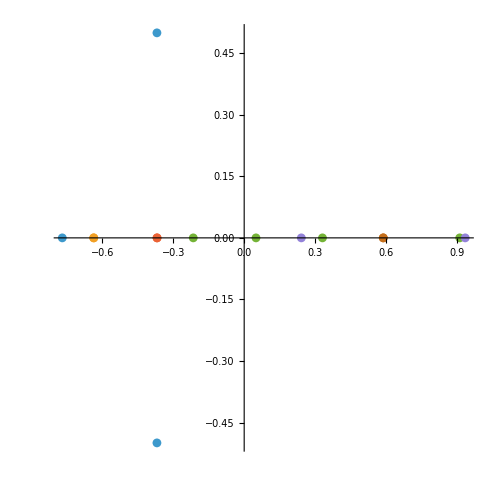

```mathematica
ComplexListPlot[betheRoots,AspectRatio->1]
```

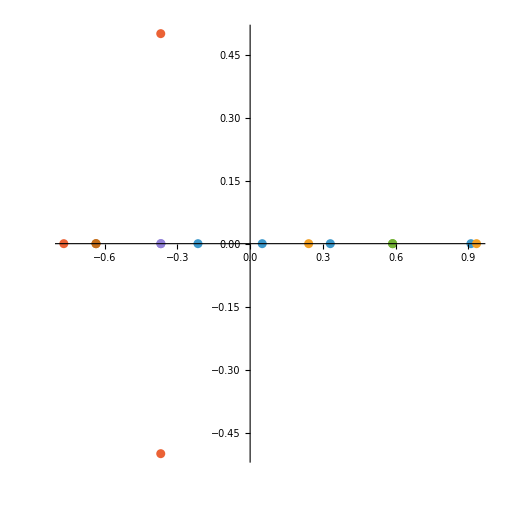

```mathematica
ComplexListPlot[betheRoots,AspectRatio->1]
```